```mathematica
x = 3
```

```mathematica
3
```

```mathematica
y =2
```

2

```mathematica
x+y
```

5

```mathematica
x^2+y^2
```

13

```mathematica
x+y
```

5

```mathematica
x/y
```

3/2

```mathematica
Sqrt[5]
Sqrt[5.]
Exp[3]
Exp[3.]
Log[4.3]
Sin[Pi/3]
Sin[Pi/3.]
```

√5

2.23607

ⅇ^3

20.0855

1.45862

(√3)/2

0.866025

```mathematica
f[x_]:=x^2+0.8
f[3]
```

9.8

```mathematica
f[Pi]
```

10.6696

```mathematica
f[1+t]
```

0.8+(1+t)^2

```mathematica
f[Sin[t*Pi]]
```

0.8+Sin[π t]^2

```mathematica
f[a_]:= Sin[a^2]+Cos[a]
f[1]
```

Cos[1]+Sin[1]

```mathematica
f[1.]
```

1.38177

```mathematica
f[1.*Pi]
```

-1.4303

```mathematica
f5[u_,v_]:= u/v
```

```mathematica
f5[21,5]
```

21/5

```mathematica
f5[21.,5]
```

4.2

```mathematica
f6[a_]:=a^2
```

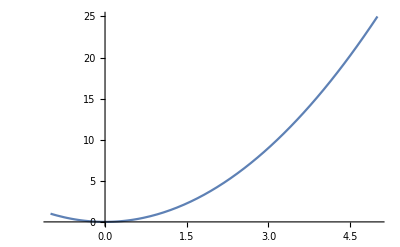

```mathematica
Plot[f6[a],{a,-1,5}]
```

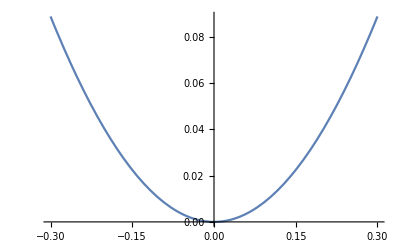

```mathematica
Plot[x*Sin[x],{x,-0.3,0.3}]
```

```mathematica
f811[x_]:=Sin[x^2]
```

```mathematica
f821[x_]:= Cos[x^2]
```

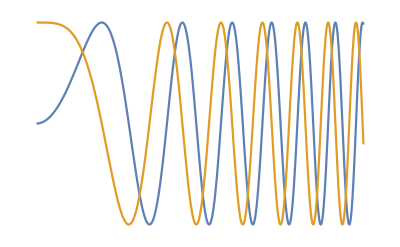

```mathematica
Plot[{f811[x],f821[x]},{x,0,2Pi},Axes->False]
```

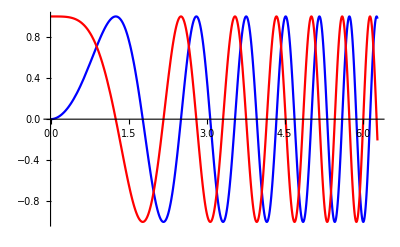

```mathematica
Plot[{f811[x],f821[x]},{x,0,2Pi},Axes->True,PlotStyle->{Blue,Red},BaseStyle->{FontSize->14}]
```

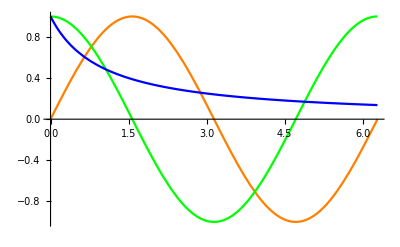

```mathematica
f91[x_]:=Sin[x]
f92[x_]:=Cos[x]
f93[x_]:=1/(x+1)
Plot[{f91[x],f92[x],f93[x]},{x,0,2Pi},PlotStyle->{Orange,Green,Blue}]
```

```mathematica
x10[t_]:=Cos[7t]Cos[11t]
y10[t_]:=Cos[7t]Sin[11t]
p10[t_]:={x10[t],y10[t]}
```

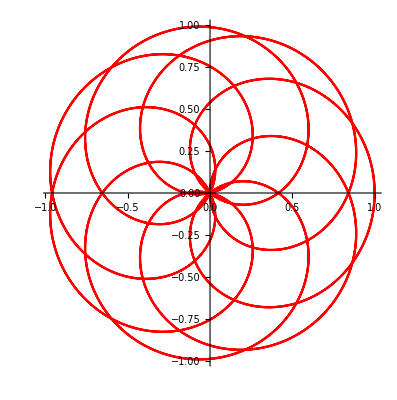

```mathematica
ParametricPlot[p10[t],{t,0,2Pi},PlotStyle->Red]
```

```mathematica
x111[t_]:=Sin[t]
y111[t_]:=Cos[t^4]
p111[t_]:={x111[t],y111[t]}
x112[t_]:=Sin[t^2]
y112[t_]:=Cos[11*t]+Sqrt[t]
p112[t_]:={x112[t],y112[t]}
```

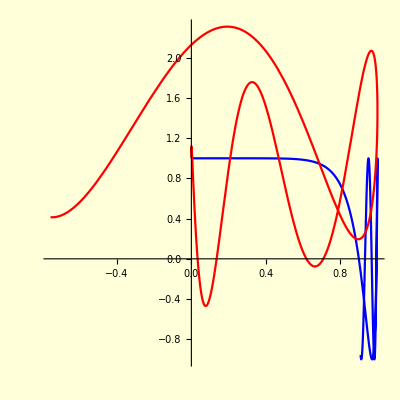

```mathematica
ParametricPlot[{p111[t],p112[t]},{t,0,2},PlotStyle->{Blue,Red},Background->LightYellow,AspectRatio->1]
```

```mathematica
G ={{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}
```

{{1,1},{1,2},{1,-1},{2,7},{3,10},{4,-9},{8,-1},{9.5,-0.8},{10,2}}

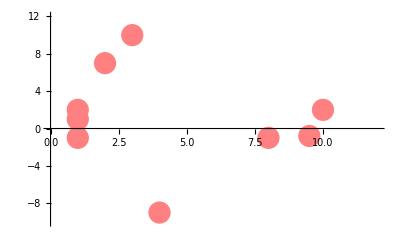

```mathematica
Plot1 =ListPlot[G,PlotStyle->{PointSize[0.04],Pink},PlotRange->{{0,12},{-10,12}}]
```

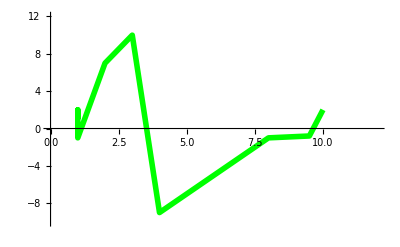

```mathematica
Plot2=ListPlot[G,Joined->True,PlotStyle->{Green,Thickness[0.01]},PlotRange->{{0,12},{-10,12}}]
```

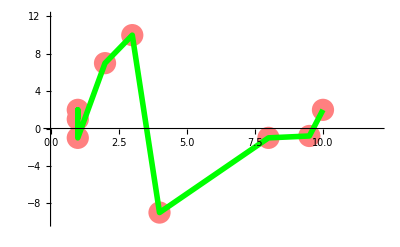

```mathematica
Show[Plot1,Plot2]
```

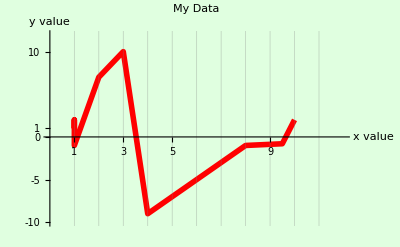

```mathematica
ListPlot[G,PlotRange->{{0,12},{-10,12}},Background->LightGreen,Joined->True,PlotStyle->{Red,Thickness[0.01]},GridLines->{{1,2,3,4,5,6,7,8,9,10,11},Automatic},Ticks->{{1,3,5,9},{-10,-5,0,1,10}},BaseStyle->{Medium,FontFamily->"Times",FontSize->10},AxesLabel->{"x value","y value"},PlotLabel->"My Data"]
```

```mathematica
f16[x_,n_]:=Cos[n x]
```

```mathematica
Animate[Plot[f16[x,n],{x,0,2Pi}],{n,1,6,1},AnimationRunning->False]
```

```mathematica
f171[x_,n_]:=Cos[n x/10]
f172[x_,n_]:= Sin[n^2 x]
```

```mathematica
Animate[Plot[{f171[x,n],f172[x,n]},{x,0,5Pi}],{n,1,10}]
```

```mathematica
xp[t_,n_]:=Sin[(2t)*n]
yp[t_,n_]:=Cos[t^2*n]
```

```mathematica
p18[t_,n_]:={xp[t,n],yp[t,n]}
```

```mathematica
Animate[ParametricPlot[p18[t,n],{t,0,5},PlotPoints->100],{n,1,10}]
```

```mathematica
f19[x_,y_]:=Sin[x^2-y^2]
Plot3D[f19[x,y],{x,-1,3},{y,-2,2},PlotPoints->{40,40},Mesh->True,AxesLabel->{"Length","Width","Height"}]
```

-Graphics3D-

```mathematica
f20[x_,y_]:=Sin[x^2-y^2]
Plot3D[f20[x,y],{x,-1,3},{y,-2,2},PlotPoints->{20,10},Mesh->False,AxesLabel->{"Length","Width","Height"}, BoxRatios->{1,1,1.5},PlotStyle->{Opacity[0.5],RGBColor[0,0,0.86]}]
```

-Graphics3D-

```mathematica
f21[x_,y_,n_]:=Sin[x+y*n]
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotPoints->40,PlotLabel->"Animation"],{n,1,15},AnimationRunning->False]
```

```mathematica
Animate[Plot3D[f21[x,y,n],{x,0,4},{y,0,2},PlotStyle->Blue ,PlotPoints->40,PlotLabel->"Animation"],{n,1,15},AnimationRunning->False]
```

```mathematica
x22[u_]:=Sin[u]
y22[u_]:=Cos[u]
z22[u_]:=u/10
spiral[u_]:={x22[u],y22[u],z22[u]}
```

```mathematica
ParametricPlot3D[spiral[u],{u,0,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[spiral[u],{u,0,20},PlotStyle->{Red,Thickness[0.05]},AxesLabel->"ParametricPlot3D"]
```

-Graphics3D-

```mathematica
x23[u_,v_]:=u
y23[u_,v_]:=v
z23[u_,v_,n_]:=n*(u^2+v^2)/10
```

```mathematica
p23[u_,v_,n_]:={x23[u,v],y23[u,v],z23[u,v,n]}
```

```mathematica
Animate[ParametricPlot3D[p23[u,v,n],{u,-5,5},{v,-5,5},PlotRange->{{-5,5},{-5,5},{0,10}},PlotPoints->30],{n,1,3,0.1}]
```